```mathematica
SetDirectory["/Users/vsvh/docs/research/comm_patterns_git"]
```

/Users/vsvh/docs/research/comm_patterns_git

```mathematica
data = Import["/Users/vsvh/docs/research/commpatterns/data/contour.dat"]
```

{{0,1.,1},{0,1.,2},{0,1.,3},{0,0.852853,4},{0,0.732733,5},{0,0.627628,6},{0,0.593093,7},{0,0.551051,8},{0,0.512012,9},{0,0.484985,10},{0,0.447447,11},{0,0.415916,12},{0,0.373874,13},{0,0.331832,14},{0,0.282282,15},{0,0.216216,16},{0,0.159159,17},{0,0.112613,18},{0,0.0675676,19},{0,0.00750751,20},{1,1.,1},{1,1.,2},{1,1.,3},{1,0.928017,4},{1,0.837685,5},{1,0.745236,6},{1,0.712773,7},{1,0.675371,8},{1,0.654199,9},{1,0.608327,10},{1,0.583627,11},{1,0.538462,12},{1,0.460833,13},{1,0.396613,14},{1,0.331687,15},{1,0.249118,16},{1,0.1729,17},{1,0.122089,18},{1,0.0677488,19},{1,0.00705716,20},{2,1.,1},{2,1.,2},{2,1.,3},{2,0.962299,4},{2,0.92046,5},{2,0.847356,6},{2,0.796322,7},{2,0.774253,8},{2,0.732874,9},{2,0.685517,10},{2,0.663448,11},{2,0.64092,12},{2,0.572874,13},{2,0.512644,14},{2,0.452414,15},{2,0.364138,16},{2,0.238621,17},{2,0.144368,18},{2,0.08,19},{2,0.0225287,20},{3,1.,1},{3,1.,2},{3,1.,3},{3,0.990722,4},{3,0.954124,5},{3,0.881443,6},{3,0.84433,7},{3,0.839691,8},{3,0.807732,9},{3,0.770619,10},{3,0.73866,11},{3,0.703093,12},{3,0.682474,13},{3,0.614433,14},{3,0.529381,15},{3,0.375773,16},{3,0.203608,17},{3,0.103608,18},{3,0.0649485,19},{3,0.00463918,20}}

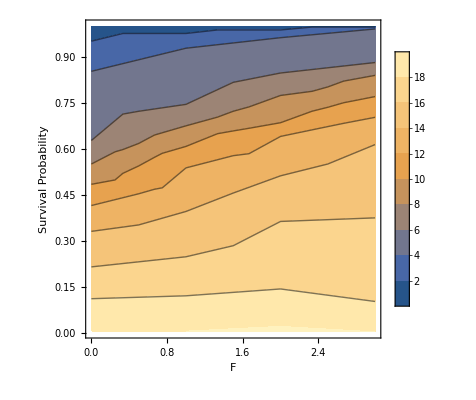

```mathematica
ListContourPlot[data,PlotLegends->{Automatic}, FrameLabel->{"F", "Survival Probability"}]
```

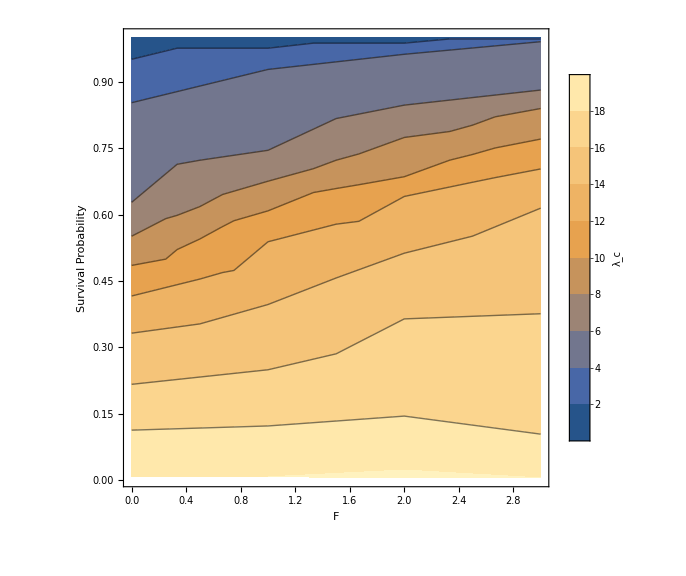

Thread::tdlen: Objects of unequal length in {{\"\<x\>\", \"\<y\>\", \"\<z\>\"}, {1, 1., 0}, {2, 1., 0}, {3, 1., 0}, {4, 0.852853, 0}, {5, 0.732733, 0}, {6, 0.627628, 0}, {7, 0.593093, 0}, {8, 0.551051, 0}, {9, 0.512012, 0}, «71»}\\\ {1} cannot be combined.

```mathematica
pc = ListContourPlot[data,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"\[\Lambda]_c",LabelStyle->{ Italic,FontFamily->"Helvetica", FontSize->20}],Right], FrameLabel->{"F", "Survival Probability"}, LabelStyle->{FontFamily->"Helvetica", FontSize->18}, ImageSize->Large]
```

```mathematica
Export["~/Desktop/contour.png", pc]
```

~/Desktop/contour.png